```mathematica
sundaram[n_] :=
Module[{L = Range[n],i=1,j},
While[3 i^2 <= n,
If[L[[i]] != "REMOVIDO",
Do[L[[j]]="REMOVIDO", {j,3i+1,n,2i+1}]];
i = i+1
];
Table[If[x!= "REMOVIDO", 2x+1, Nothing], {x,L}]]
```

```mathematica
redundancia[n_] :=
Module[{L = Range[n],i=1,j, count=0},
While[3 i^2 <= n,
If[L[[i]] != "REMOVIDO",
Do[If[L[[j]]=="REMOVIDO", count++; L[[j]]="REMOVIDO2", L[[j]]="REMOVIDO"], {j,3i+1,n,2i+1}]];
i = i+1
];
count]
```

```mathematica
redundancia/@Range[10,50,10]
```

{0,1,4,6,6}

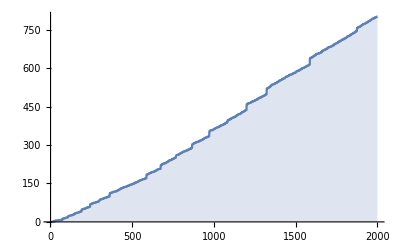

```mathematica
soverlapsplot = DiscretePlot[sundaramoverlaps[n],{n,1,2000}]
```

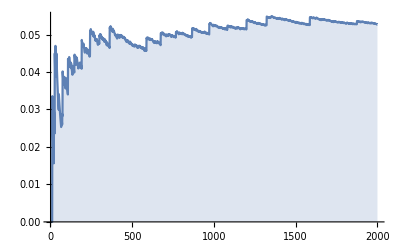

```mathematica
DiscretePlot[redundancia[n]/(n Log[n]),{n,1,2000}]
```

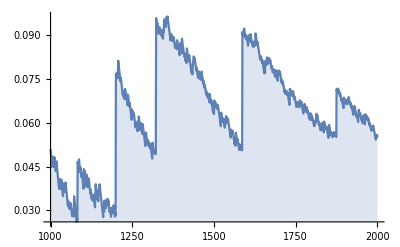

```mathematica
DiscretePlot[Abs[redundancia[n]/(.05 n Log[n]) - 1],{n,1000,2000}]
```

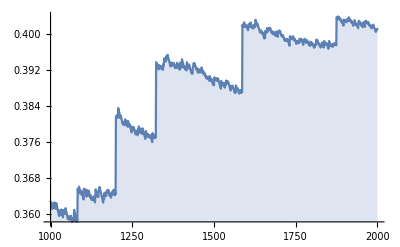

```mathematica
DiscretePlot[redundancia[n]/(n ),{n,1000,2000}]
```

```mathematica
soverlapslist = Map[sundaramoverlaps, Range[2000]];
```

```mathematica
sdeltas = soverlapslist[[2;;]]-soverlapslist[[;;-2]];
```

```mathematica
Table[If[soverlapslist[[i+1]]-soverlapslist[[i]]>7, i, Nothing],{i,Length[soverlapslist]-1}]
```

{191,242,362,587,674,971,1199,1322,1586}

```mathematica
FactorInteger[2 191 -1]
```

{{3,1},{127,1}}

```mathematica
3*5*7
```

105

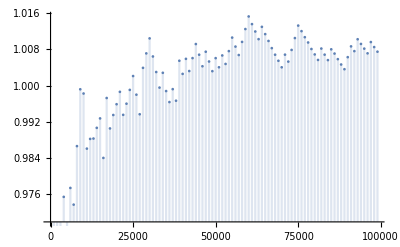

```mathematica
DiscretePlot[16 sundaramoverlaps[n]/(n Log[n]),{n,1,100000,1000}]
```

```mathematica
.063 * 15
```

0.945

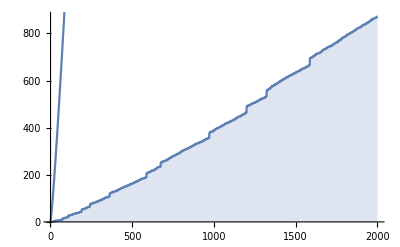

```mathematica
Show[soverlapsplot,Plot[(2x+1) Log[2x+1] ,{x,0,2000}]]
```

```mathematica
foo[n_] := Length[sundaram[n]] Log[n]/n
```

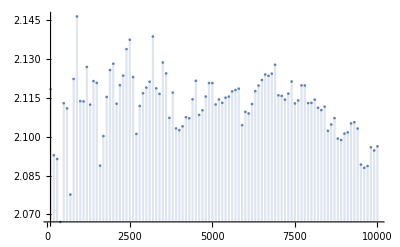

2.09627

```mathematica
DiscretePlot[foo[n],{n,100,10000,100}]
```

```mathematica
foo/@(10^Range[7])//N
```

{1.61181,2.11838,2.11377,2.09627,2.09478,2.07564,2.06426}

```mathematica
sundaram[30]
```

{3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61}

```mathematica
1.5(11+1.5 23)
```

68.25

```mathematica
stime[n_] := AbsoluteTiming[sundaram[n]][[1]]
```

```mathematica
Table[stime[n],{n,1,100}]
```

{0.0000529,0.0000238,0.0000276,0.0000426,0.0000297,0.0000289,0.0000312,0.0000333,0.0000338,0.0000366,0.0000362,0.000048,0.0000491,0.0000404,0.0000409,0.0000442,0.0000448,0.0000466,0.0000532,0.0000506,0.0000502,0.0000547,0.0000548,0.0000553,0.000058,0.000058,0.0000695,0.0000691,0.0000708,0.000076,0.0000835,0.0000777,0.0000794,0.0000819,0.0000807,0.0000815,0.0000868,0.0000899,0.0000882,0.0000905,0.0000921,0.0000944,0.000096,0.000097,0.0000995,0.0001033,0.0001033,0.0001072,0.0001098,0.0001099,0.0001113,0.0001157,0.0001149,0.0001175,0.0001203,0.0001203,0.0001223,0.0001256,0.0001259,0.0001285,0.0001287,0.0001329,0.0001316,0.0001341,0.0001339,0.0001374,0.0002081,0.0002154,0.0002609,0.0001519,0.0001482,0.0001826,0.0001559,0.0001614,0.0001692,0.0001701,0.000174,0.0001757,0.0001761,0.000204,0.0002152,0.000224,0.0002247,0.0002243,0.0002254,0.0002312,0.0002371,0.0002374,0.0002362,0.0002403,0.0002372,0.0001689,0.0001529,0.0001578,0.0001562,0.000157,0.0001584,0.0001653,0.0001636,0.0001651}

```mathematica
times =Table[{n,stime[n]},{n,10^3, 10^5, 10^3}]
```

{{1000,0.0012668},{2000,0.0031016},{3000,0.0035487},{4000,0.00424},{5000,0.0052182},{6000,0.0070907},{7000,0.0073401},{8000,0.008437},{9000,0.0095938},{10000,0.0105604},{11000,0.0116681},{12000,0.0127973},{13000,0.0142133},{14000,0.0178218},{15000,0.0164031},{16000,0.0187424},{17000,0.0232021},{18000,0.0201391},{19000,0.0241179},{20000,0.0248373},{21000,0.0301336},{22000,0.0233139},{23000,0.0298937},{24000,0.031588},{25000,0.0328704},{26000,0.0351933},{27000,0.0384919},{28000,0.0393134},{29000,0.0361643},{30000,0.0359423},{31000,0.0409553},{32000,0.0480015},{33000,0.0362375},{34000,0.0415696},{35000,0.0461373},{36000,0.0429113},{37000,0.0402373},{38000,0.0502538},{39000,0.0539636},{40000,0.0501948},{41000,0.0493174},{42000,0.0535142},{43000,0.0589269},{44000,0.049505},{45000,0.0550738},{46000,0.0548742},{47000,0.0560617},{48000,0.0652073},{49000,0.0638575},{50000,0.0688377},{51000,0.0630789},{52000,0.0588529},{53000,0.0692229},{54000,0.0693305},{55000,0.0795771},{56000,0.0796864},{57000,0.0719226},{58000,0.0691149},{59000,0.0707936},{60000,0.0888179},{61000,0.0755871},{62000,0.0855708},{63000,0.0748204},{64000,0.0792824},{65000,0.0970391},{66000,0.0862902},{67000,0.0964483},{68000,0.0906147},{69000,0.0785271},{70000,0.100305},{71000,0.0952686},{72000,0.089797},{73000,0.0920397},{74000,0.0933705},{75000,0.100928},{76000,0.109078},{77000,0.105444},{78000,0.0971275},{79000,0.113419},{80000,0.10535},{81000,0.101468},{82000,0.107582},{83000,0.107277},{84000,0.0994089},{85000,0.109955},{86000,0.115207},{87000,0.117657},{88000,0.115935},{89000,0.124647},{90000,0.122141},{91000,0.114492},{92000,0.124251},{93000,0.122543},{94000,0.124989},{95000,0.123421},{96000,0.124325},{97000,0.136124},{98000,0.139131},{99000,0.127285},{100000,0.141455}}

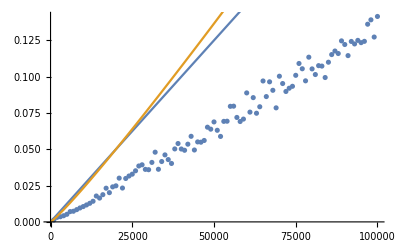

```mathematica
Show[
ListPlot[times],
Plot[{(.05 / 20000) n ,(.05 / 20000) n Log[n]/Log[20000]} ,{n,0,10^5}]
]
```